{112,118,132,129,121,135,148,148,136,119,104,118,115,126,141,135,125,149,170,170,158,133,114,140,145,150,178,163,172,178,199,199,184,162,146,166,171,180,193,181,183,218,230,242,209,191,172,194,196,196,236,235,229,243,264,272,237,211,180,201,204,188,235,227,234,264,302,293,259,229,203,229,242,233,267,269,270,315,364,347,312,274,237,278,284,277,317,313,318,374,413,405,355,306,271,306,315,301,356,348,355,422,465,467,404,347,305,336,340,318,362,348,363,435,491,505,404,359,310,337,360,342,406,396,420,472,548,559,463,407,362,405,417,391,419,461,472,535,622,606,508,461,390,432}

{{1,112},{2,118},{3,132},{4,129},{5,121},{6,135},{7,148},{8,148},{9,136},{10,119},{11,104},{12,118},{13,115},{14,126},{15,141},{16,135},{17,125},{18,149},{19,170},{20,170},{21,158},{22,133},{23,114},{24,140},{25,145},{26,150},{27,178},{28,163},{29,172},{30,178},{31,199},{32,199},{33,184},{34,162},{35,146},{36,166},{37,171},{38,180},{39,193},{40,181},{41,183},{42,218},{43,230},{44,242},{45,209},{46,191},{47,172},{48,194},{49,196},{50,196},{51,236},{52,235},{53,229},{54,243},{55,264},{56,272},{57,237},{58,211},{59,180},{60,201},{61,204},{62,188},{63,235},{64,227},{65,234},{66,264},{67,302},{68,293},{69,259},{70,229},{71,203},{72,229},{73,242},{74,233},{75,267},{76,269},{77,270},{78,315},{79,364},{80,347},{81,312},{82,274},{83,237},{84,278},{85,284},{86,277},{87,317},{88,313},{89,318},{90,374},{91,413},{92,405},{93,355},{94,306},{95,271},{96,306},{97,315},{98,301},{99,356},{100,348},{101,355},{102,422},{103,465},{104,467},{105,404},{106,347},{107,305},{108,336},{109,340},{110,318},{111,362},{112,348},{113,363},{114,435},{115,491},{116,505},{117,404},{118,359},{119,310},{120,337},{121,360},{122,342},{123,406},{124,396},{125,420},{126,472},{127,548},{128,559},{129,463},{130,407},{131,362},{132,405},{133,417},{134,391},{135,419},{136,461},{137,472},{138,535},{139,622},{140,606},{141,508},{142,461},{143,390},{144,432}}

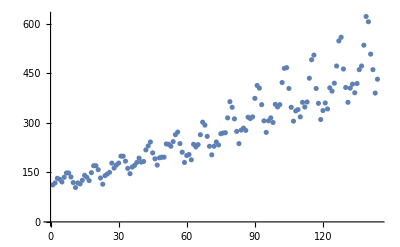

```mathematica
data={112,118,132,129,121,135,148,148,136,119,104,118,115,126,141,135,125,149,170,170,158,133,114,140,145,150,178,163,172,178,199,199,184,162,146,166,171,180,193,181,183,218,230,242,209,191,172,194,196,196,236,235,229,243,264,272,237,211,180,201,204,188,235,227,234,264,302,293,259,229,203,229,242,233,267,269,270,315,364,347,312,274,237,278,284,277,317,313,318,374,413,405,355,306,271,306,315,301,356,348,355,422,465,467,404,347,305,336,340,318,362,348,363,435,491,505,404,359,310,337,360,342,406,396,420,472,548,559,463,407,362,405,417,391,419,461,472,535,622,606,508,461,390,432}

KU={};

Do[AppendTo[KU,{j,data[[j]]}];
,{j,1,Length[data]}];
KU
AIRPASSENGERSDATA=ListPlot[KU]
```

```mathematica
training=RandomSample[List/@Most[#]->List@Last[#]&/@(Partition[data,11,1])]
```

{{{148},{136},{119},{104},{118},{115},{126},{141},{135},{125}}→{149},{{191},{172},{194},{196},{196},{236},{235},{229},{243},{264}}→{272},{{230},{242},{209},{191},{172},{194},{196},{196},{236},{235}}→{229},{{171},{180},{193},{181},{183},{218},{230},{242},{209},{191}}→{172},{{204},{188},{235},{227},{234},{264},{302},{293},{259},{229}}→{203},{{237},{211},{180},{201},{204},{188},{235},{227},{234},{264}}→{302},{{363},{435},{491},{505},{404},{359},{310},{337},{360},{342}}→{406},{{201},{204},{188},{235},{227},{234},{264},{302},{293},{259}}→{229},{{188},{235},{227},{234},{264},{302},{293},{259},{229},{203}}→{229},{{306},{315},{301},{356},{348},{355},{422},{465},{467},{404}}→{347},{{118},{115},{126},{141},{135},{125},{149},{170},{170},{158}}→{133},{{348},{363},{435},{491},{505},{404},{359},{310},{337},{360}}→{342},{{149},{170},{170},{158},{133},{114},{140},{145},{150},{178}}→{163},{{391},{419},{461},{472},{535},{622},{606},{508},{461},{390}}→{432},{{413},{405},{355},{306},{271},{306},{315},{301},{356},{348}}→{355},{{422},{465},{467},{404},{347},{305},{336},{340},{318},{362}}→{348},{{404},{359},{310},{337},{360},{342},{406},{396},{420},{472}}→{548},{{284},{277},{317},{313},{318},{374},{413},{405},{355},{306}}→{271},{{178},{163},{172},{178},{199},{199},{184},{162},{146},{166}}→{171},{{209},{191},{172},{194},{196},{196},{236},{235},{229},{243}}→{264},{{136},{119},{104},{118},{115},{126},{141},{135},{125},{149}}→{170},{{196},{236},{235},{229},{243},{264},{272},{237},{211},{180}}→{201},{{420},{472},{548},{559},{463},{407},{362},{405},{417},{391}}→{419},{{270},{315},{364},{347},{312},{274},{237},{278},{284},{277}}→{317},{{347},{312},{274},{237},{278},{284},{277},{317},{313},{318}}→{374},{{237},{278},{284},{277},{317},{313},{318},{374},{413},{405}}→{355},{{242},{209},{191},{172},{194},{196},{196},{236},{235},{229}}→{243},{{269},{270},{315},{364},{347},{312},{274},{237},{278},{284}}→{277},{{362},{405},{417},{391},{419},{461},{472},{535},{622},{606}}→{508},{{193},{181},{183},{218},{230},{242},{209},{191},{172},{194}}→{196},{{404},{347},{305},{336},{340},{318},{362},{348},{363},{435}}→{491},{{306},{271},{306},{315},{301},{356},{348},{355},{422},{465}}→{467},{{264},{302},{293},{259},{229},{203},{229},{242},{233},{267}}→{269},{{229},{242},{233},{267},{269},{270},{315},{364},{347},{312}}→{274},{{315},{301},{356},{348},{355},{422},{465},{467},{404},{347}}→{305},{{318},{374},{413},{405},{355},{306},{271},{306},{315},{301}}→{356},{{234},{264},{302},{293},{259},{229},{203},{229},{242},{233}}→{267},{{356},{348},{355},{422},{465},{467},{404},{347},{305},{336}}→{340},{{172},{178},{199},{199},{184},{162},{146},{166},{171},{180}}→{193},{{264},{272},{237},{211},{180},{201},{204},{188},{235},{227}}→{234},{{229},{203},{229},{242},{233},{267},{269},{270},{315},{364}}→{347},{{360},{342},{406},{396},{420},{472},{548},{559},{463},{407}}→{362},{{406},{396},{420},{472},{548},{559},{463},{407},{362},{405}}→{417},{{126},{141},{135},{125},{149},{170},{170},{158},{133},{114}}→{140},{{125},{149},{170},{170},{158},{133},{114},{140},{145},{150}}→{178},{{472},{548},{559},{463},{407},{362},{405},{417},{391},{419}}→{461},{{559},{463},{407},{362},{405},{417},{391},{419},{461},{472}}→{535},{{229},{243},{264},{272},{237},{211},{180},{201},{204},{188}}→{235},{{135},{148},{148},{136},{119},{104},{118},{115},{126},{141}}→{135},{{505},{404},{359},{310},{337},{360},{342},{406},{396},{420}}→{472},{{312},{274},{237},{278},{284},{277},{317},{313},{318},{374}}→{413},{{242},{233},{267},{269},{270},{315},{364},{347},{312},{274}}→{237},{{467},{404},{347},{305},{336},{340},{318},{362},{348},{363}}→{435},{{396},{420},{472},{548},{559},{463},{407},{362},{405},{417}}→{391},{{301},{356},{348},{355},{422},{465},{467},{404},{347},{305}}→{336},{{435},{491},{505},{404},{359},{310},{337},{360},{342},{406}}→{396},{{491},{505},{404},{359},{310},{337},{360},{342},{406},{396}}→{420},{{364},{347},{312},{274},{237},{278},{284},{277},{317},{313}}→{318},{{170},{170},{158},{133},{114},{140},{145},{150},{178},{163}}→{172},{{104},{118},{115},{126},{141},{135},{125},{149},{170},{170}}→{158},{{141},{135},{125},{149},{170},{170},{158},{133},{114},{140}}→{145},{{362},{348},{363},{435},{491},{505},{404},{359},{310},{337}}→{360},{{145},{150},{178},{163},{172},{178},{199},{199},{184},{162}}→{146},{{194},{196},{196},{236},{235},{229},{243},{264},{272},{237}}→{211},{{118},{132},{129},{121},{135},{148},{148},{136},{119},{104}}→{118},{{184},{162},{146},{166},{171},{180},{193},{181},{183},{218}}→{230},{{465},{467},{404},{347},{305},{336},{340},{318},{362},{348}}→{363},{{463},{407},{362},{405},{417},{391},{419},{461},{472},{535}}→{622},{{227},{234},{264},{302},{293},{259},{229},{203},{229},{242}}→{233},{{170},{158},{133},{114},{140},{145},{150},{178},{163},{172}}→{178},{{277},{317},{313},{318},{374},{413},{405},{355},{306},{271}}→{306},{{135},{125},{149},{170},{170},{158},{133},{114},{140},{145}}→{150},{{196},{196},{236},{235},{229},{243},{264},{272},{237},{211}}→{180},{{318},{362},{348},{363},{435},{491},{505},{404},{359},{310}}→{337},{{355},{306},{271},{306},{315},{301},{356},{348},{355},{422}}→{465},{{405},{355},{306},{271},{306},{315},{301},{356},{348},{355}}→{422},{{203},{229},{242},{233},{267},{269},{270},{315},{364},{347}}→{312},{{236},{235},{229},{243},{264},{272},{237},{211},{180},{201}}→{204},{{243},{264},{272},{237},{211},{180},{201},{204},{188},{235}}→{227},{{305},{336},{340},{318},{362},{348},{363},{435},{491},{505}}→{404},{{359},{310},{337},{360},{342},{406},{396},{420},{472},{548}}→{559},{{166},{171},{180},{193},{181},{183},{218},{230},{242},{209}}→{191},{{158},{133},{114},{140},{145},{150},{178},{163},{172},{178}}→{199},{{181},{183},{218},{230},{242},{209},{191},{172},{194},{196}}→{196},{{342},{406},{396},{420},{472},{548},{559},{463},{407},{362}}→{405},{{218},{230},{242},{209},{191},{172},{194},{196},{196},{236}}→{235},{{121},{135},{148},{148},{136},{119},{104},{118},{115},{126}}→{141},{{278},{284},{277},{317},{313},{318},{374},{413},{405},{355}}→{306},{{163},{172},{178},{199},{199},{184},{162},{146},{166},{171}}→{180},{{133},{114},{140},{145},{150},{178},{163},{172},{178},{199}}→{199},{{313},{318},{374},{413},{405},{355},{306},{271},{306},{315}}→{301},{{405},{417},{391},{419},{461},{472},{535},{622},{606},{508}}→{461},{{271},{306},{315},{301},{356},{348},{355},{422},{465},{467}}→{404},{{211},{180},{201},{204},{188},{235},{227},{234},{264},{302}}→{293},{{199},{184},{162},{146},{166},{171},{180},{193},{181},{183}}→{218},{{315},{364},{347},{312},{274},{237},{278},{284},{277},{317}}→{313},{{235},{229},{243},{264},{272},{237},{211},{180},{201},{204}}→{188},{{407},{362},{405},{417},{391},{419},{461},{472},{535},{622}}→{606},{{150},{178},{163},{172},{178},{199},{199},{184},{162},{146}}→{166},{{115},{126},{141},{135},{125},{149},{170},{170},{158},{133}}→{114},{{417},{391},{419},{461},{472},{535},{622},{606},{508},{461}}→{390},{{293},{259},{229},{203},{229},{242},{233},{267},{269},{270}}→{315},{{336},{340},{318},{362},{348},{363},{435},{491},{505},{404}}→{359},{{355},{422},{465},{467},{404},{347},{305},{336},{340},{318}}→{362},{{337},{360},{342},{406},{396},{420},{472},{548},{559},{463}}→{407},{{199},{199},{184},{162},{146},{166},{171},{180},{193},{181}}→{183},{{119},{104},{118},{115},{126},{141},{135},{125},{149},{170}}→{170},{{348},{355},{422},{465},{467},{404},{347},{305},{336},{340}}→{318},{{172},{194},{196},{196},{236},{235},{229},{243},{264},{272}}→{237},{{162},{146},{166},{171},{180},{193},{181},{183},{218},{230}}→{242},{{274},{237},{278},{284},{277},{317},{313},{318},{374},{413}}→{405},{{259},{229},{203},{229},{242},{233},{267},{269},{270},{315}}→{364},{{235},{227},{234},{264},{302},{293},{259},{229},{203},{229}}→{242},{{114},{140},{145},{150},{178},{163},{172},{178},{199},{199}}→{184},{{112},{118},{132},{129},{121},{135},{148},{148},{136},{119}}→{104},{{317},{313},{318},{374},{413},{405},{355},{306},{271},{306}}→{315},{{180},{201},{204},{188},{235},{227},{234},{264},{302},{293}}→{259},{{178},{199},{199},{184},{162},{146},{166},{171},{180},{193}}→{181},{{272},{237},{211},{180},{201},{204},{188},{235},{227},{234}}→{264},{{146},{166},{171},{180},{193},{181},{183},{218},{230},{242}}→{209},{{347},{305},{336},{340},{318},{362},{348},{363},{435},{491}}→{505},{{310},{337},{360},{342},{406},{396},{420},{472},{548},{559}}→{463},{{302},{293},{259},{229},{203},{229},{242},{233},{267},{269}}→{270},{{183},{218},{230},{242},{209},{191},{172},{194},{196},{196}}→{236},{{180},{193},{181},{183},{218},{230},{242},{209},{191},{172}}→{194},{{374},{413},{405},{355},{306},{271},{306},{315},{301},{356}}→{348},{{233},{267},{269},{270},{315},{364},{347},{312},{274},{237}}→{278},{{140},{145},{150},{178},{163},{172},{178},{199},{199},{184}}→{162},{{340},{318},{362},{348},{363},{435},{491},{505},{404},{359}}→{310},{{129},{121},{135},{148},{148},{136},{119},{104},{118},{115}}→{126},{{548},{559},{463},{407},{362},{405},{417},{391},{419},{461}}→{472},{{148},{148},{136},{119},{104},{118},{115},{126},{141},{135}}→{125},{{132},{129},{121},{135},{148},{148},{136},{119},{104},{118}}→{115},{{267},{269},{270},{315},{364},{347},{312},{274},{237},{278}}→{284}}

```mathematica
net=NetChain[{GatedRecurrentLayer[10],LinearLayer[1]},"Input"->{10,1},"Output"->1]
```

NetChain[<>]

```mathematica
trained=NetTrain[net,training]
```

NetChain[<>]

```mathematica
trained[{{146},{166},{171},{180},{193},{181},{183},{218},{230},{242}}]
```

{170.426}

```mathematica
trained[{{413},{405},{355},{306},{271},{306},{315},{301},{356},{348}}]
```

{419.099}

```mathematica
KARA={};

Do[ten[j]=Transpose[{data[[j;;j+9]]}];
POINT[j+1]=Flatten[{j+10,trained[ten[j]]}];
AppendTo[KARA,POINT[j+1]];
,{j,1,Length[data]-9}];
```

```mathematica
KARA
```

{{11,146.005},{12,148.384},{13,154.043},{14,152.733},{15,149.675},{16,155.523},{17,161.826},{18,161.324},{19,154.8},{20,147.85},{21,143.635},{22,148.877},{23,148.572},{24,153.2},{25,160.169},{26,157.611},{27,153.988},{28,165.515},{29,178.668},{30,178.141},{31,169.697},{32,157.038},{33,151.441},{34,163.134},{35,166.81},{36,170.5},{37,189.143},{38,178.864},{39,185.394},{40,190.085},{41,207.775},{42,206.798},{43,192.736},{44,177.253},{45,170.426},{46,184.077},{47,189.317},{48,197.348},{49,208.88},{50,200.503},{51,203.552},{52,235.355},{53,247.444},{54,259.421},{55,222.652},{56,207.497},{57,196.816},{58,216.477},{59,221.142},{60,224.186},{61,262.242},{62,261.353},{63,255.581},{64,269.731},{65,290.607},{66,296.684},{67,254.847},{68,227.914},{69,205.544},{70,226.362},{71,232.893},{72,225.62},{73,267.634},{74,262.544},{75,271.188},{76,300.107},{77,334.947},{78,323.594},{79,286.488},{80,257.585},{81,240.766},{82,268.237},{83,284.111},{84,281.457},{85,312.74},{86,316.931},{87,320.468},{88,356.87},{89,391.209},{90,377.742},{91,347.895},{92,314.234},{93,286.835},{94,324.296},{95,331.825},{96,329.374},{97,361.639},{98,360.013},{99,365.182},{100,401.731},{101,419.099},{102,414.636},{103,385.555},{104,348.394},{105,323.539},{106,353.7},{107,362.646},{108,355.396},{109,393.733},{110,390.044},{111,395.554},{112,425.545},{113,435.133},{114,434.503},{115,414.878},{116,382.456},{117,353.657},{118,378.121},{119,382.336},{120,369.771},{121,399.021},{122,392.516},{123,402.519},{124,430.4},{125,439.523},{126,440.135},{127,415.804},{128,392.595},{129,362.063},{130,383.614},{131,399.563},{132,392.06},{133,423.03},{134,420.777},{135,429.228},{136,439.164},{137,444.35},{138,444.312},{139,434.974},{140,420.375},{141,402.343},{142,422.884},{143,427.846},{144,421.632},{145,431.336}}

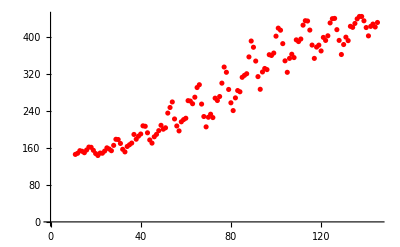

```mathematica
PREDICTIONDATA=ListPlot[KARA,PlotStyle->Red]
```

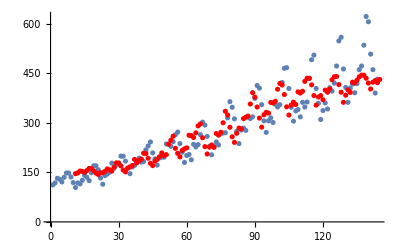

```mathematica
Show[AIRPASSENGERSDATA,PREDICTIONDATA]
```